EXTERNAL DEPENDENCIES: Evaluate the setups in model-setup.nb and shere-LSA-setup.nb first

### Setup

#### Parameter setup

```mathematica
fixedParams={
r->3.5,Dm["md"]->0.2,Dm[_]->0.01,DD->11,DG->11,DF->11,DB->11
};
```

```mathematica
Vol=4Pi/3 3.5^3;
```

```mathematica
densitiesWT={nD->8690/Vol,nG->2170/Vol,nB->1037/Vol,nF->934/Vol}
```

{nD→48.3868,nG→12.0828,nB→5.77412,nF→5.20061}

```mathematica
sampleParamNames={
ktg,kgt,
kD,
kdoff,
kfd,
kbfD,
ktD,
ktB,kb,
kbF,kbf,
kF,kf
};
numSampleParams=Length@sampleParamNames;
```

```mathematica
sampleParamDisplayNames={
Subscript[k, "tg"],Subscript[k, "gt"],Subscript[k, "D"],Subscript[k, "d"],Subscript[k, "fd"],Subscript[k, "bfD"],Subscript[k, "tD"],Subscript[k, "tB"],Subscript[k, "b"],Subscript[k, "bF"],Subscript[k, "bf"],Subscript[k, "F"],Subscript[k, "f"]
};
```

TODO: model variant with Michaelis Menten rate for Cdc42-Bem1 interaction, to buffer against strong variations in Cdc42 copy number?

```mathematica
minGrowth=10^-4;
```

```mathematica
(*parameter override, number of fixed points, condition on growth rates, first modes is index 2 *)
constraints={
(*WT*)
{{},_?Positive,Re@#[[2]]>minGrowth(*&&Re@#[[2]]>Re@#[[3]]*)&},
(* 0.2xCdc42 *)
{{nD->0.2 8690/Vol},_?Positive,Re@#[[2]]>minGrowth&} ,
(* dBem1 *)
{{nB->0},_?Positive,Re@#[[2]]<0&}, 
(* dBem1 dBem3 *)
{{nB->0,nG->(2170-600)/Vol},_?Positive,Re@#[[2]]>minGrowth&},
(* dBem1 1.5xCdc42 *)
{{nB->0,nD->1.5 8690/Vol,nG->2170/Vol},_?Positive,Re@#[[2]]>minGrowth&},
(* dBem1, grown cell *)
{{nB->0,r->7},_?Positive,Re@#[[2]]<0&}
};
```

#### Filtering setup

```mathematica
testConstraint[params_,c_,"lMax"->lMax_]:=With[{
eqs=Quiet@nSolveUniformEq[Join[c[[1]],params]]
},
If[MatchQ[Length@eqs,c[[2]]],
If[c[[3]]@findDispRel[Join[c[[1]],params],Last@eqs,lMax,"ApproxJacobian"->sphereJacobianApprox][[All,2]],
True,
"stability"
],
"numFPs"
]
];
testConstraint[params_,c_]:=testConstraint[params,c,"lMax"->1];
```

```mathematica
testConstraintsSquentially[params_,cList_]:=Block[{test=True},
Do[
If[testConstraint[params,cList[[cIndex]]]=!=True,test=False;Break[]],
{cIndex,Length@cList}
];
test
]
```

#### Visualization setup

```mathematica
roundSignificant[x_,digits_Integer]:=N@Round[x,10^(Floor[Log10@x]-digits+1)];
```

```mathematica
Options[renderParameterGrid]={"selectedParams"->None};
renderParameterGrid[paramSets_,highlightSets_:{},OptionsPattern[]]:=GraphicsGrid[Join[
Table[
If[j==0,
Style[#,FontSize->14]&@sampleParamDisplayNames[[i]],
If[j<i,
Graphics[{
If[Length@highlightSets==0,
{Black,
Point[Log10@paramSets[[All,{j,i}]]]
},
{Gray,
Point[Log10@paramSets[[All,{j,i}]]],
AbsolutePointSize[3],
Darker@Blue,
Point[Log10@highlightSets[[All,{j,i}]]]
}
],
If[OptionValue["selectedParams"]=!=None,
{Red,AbsolutePointSize[6],Point[Log10@OptionValue["selectedParams"][[{j,i}]]]}
]
},
PlotRange->{{-3,1},{-3,1}},
AspectRatio->1,
Frame->True,FrameStyle->Black,FrameTicks->False,ImagePadding->1,ImageSize->50,
GridLines->Automatic,GridLinesStyle->GrayLevel[0.75]
]
]
],{i,2,numSampleParams},{j,0,numSampleParams}
],
{Join[{""},Style[#,FontSize->14]&/@Most@sampleParamDisplayNames,{""}]}
],
Spacings->{0, 0},
Alignment->{Append[ConstantArray[Center,numSampleParams],Left]}
]
```

### Run parameter sampling

WARNING: This requires ca 240 CPU hours (10 hours on a 24 core workstation).
To load the data used in the paper, use the code in the next subsection instead.

```mathematica
LaunchKernels[];
```

```mathematica
ParallelEvaluate[Off[NSolve::sfail]];
ParallelEvaluate[Off[FindRoot::lstol]];
```

```mathematica
SetSharedFunction[ParallelSow];
ParallelSow[expr_]:=Sow[expr];
```

```mathematica
RandomSeed[1];
```

```mathematica
matchParams=Parallelize[Do[
With[{randParamSet=10^RandomReal[{-3,1},numSampleParams]},
If[testConstraintsSquentially[Join[densitiesWT,fixedParams,Thread[sampleParamNames->randParamSet]],constraints],
ParallelSow[randParamSet]
]
],
5 10^6
]]//Reap//Last//First;//AbsoluteTiming
```

{37511.4,Null}

```mathematica
Length@matchParams
```

7730

```mathematica
Put[matchParams,NotebookDirectory[]<>"Data/filtered-params_seed=1_N=5e6.txt"]
```

### Load filtered parameter sets (from sampling run over 5 10^6 parameter sets)

```mathematica
matchParams=Get[NotebookDirectory[]<>"Data/filtered-params_seed=1_N=5e6.txt"];
```

```mathematica
Length@matchParams
```

7730

```mathematica
Length@matchParams[[1]]
```

13

```mathematica
matchParams[[1]]
```

{0.704199,0.143151,0.0281306,2.80996,2.08045,1.54056,0.103567,0.00751624,0.453088,0.132511,0.013284,0.14613,8.13994}

## Parameter filtering with additional constraints

### Filter for WT first mode constraint

```mathematica
firstModeConstraint={{},1,Re@#[[2]]>0.005&&Re@#[[2]]>Re@#[[3]](*&&Re@#[[4]]*)>0&};
```

```mathematica
filteredParams["WTfirstMode"]=First@Last@Reap[ParallelDo[
If[testConstraint[Join[densitiesWT,fixedParams,Thread[sampleParamNames->paramSet]],firstModeConstraint,"lMax"->3],
ParallelSow[paramSet]
],
{paramSet,matchParams}
]
];//AbsoluteTiming
```

{42.0147,Null}

```mathematica
Length@filteredParams["WTfirstMode"]
```

1422

```mathematica
meanFilteredParams=10^Mean@Log10@filteredParams["WTfirstMode"];
```

```mathematica
meanFilteredParams
```

{0.0817411,0.222341,0.0375158,1.28618,0.114346,0.0634014,0.0547972,0.193355,0.1438,0.118414,0.110635,0.0646498,0.163477}

```mathematica
selectedParams=First@MinimalBy[filteredParams["WTfirstMode"],Norm[Log10@#-Log10@meanFilteredParams]&];
```

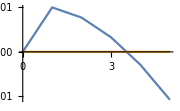
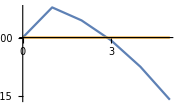
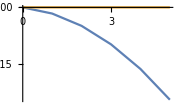
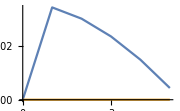
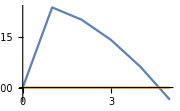
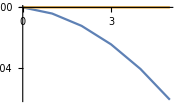
1
-Graphics-1
-Graphics-1
-Graphics-3
-Graphics-3
-Graphics-1
-Graphics-

```mathematica
Row[With[{params=Join[#,densitiesWT,fixedParams,Thread[sampleParamNames->selectedParams]]},
With[{eqs=nSolveUniformEq@params},
Column[{
Length@eqs,
ListPlot[Transpose[Thread[{#[[1]],ReIm@#[[2]]}]&/@findDispRel[Last@eqs,params,5,"ApproxJacobian"->sphereJacobianApprox
]],Joined->True,ImageSize->Small,PlotRange->All]
},Alignment->Center]
]]&/@constraints[[All,1]]]
```

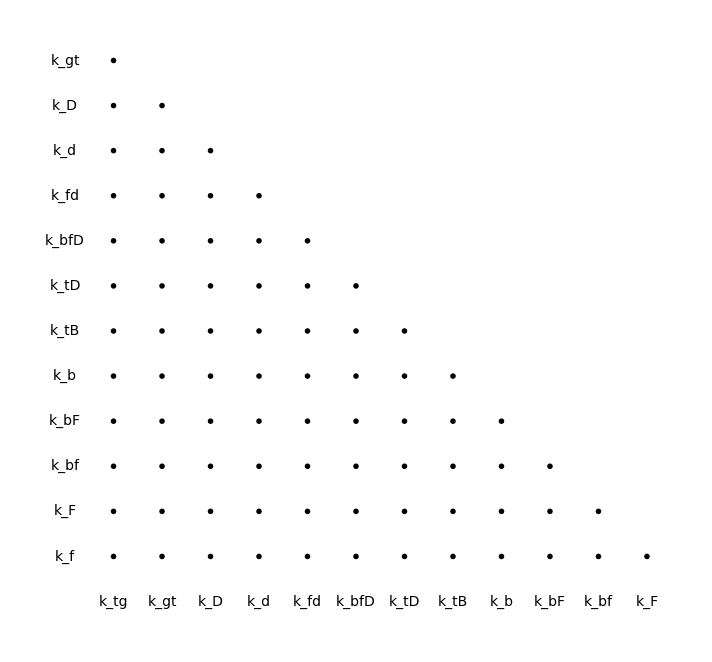

```mathematica
renderParameterGrid[filteredParams["WTfirstMode"]]
```

#### Cytosolic fractions

```mathematica
homEqTable=ParallelMap[nSolveUniformEq[Join[densitiesWT,fixedParams,Thread[sampleParamNames->#]]][[-1]]&,filteredParams["WTfirstMode"]];
```

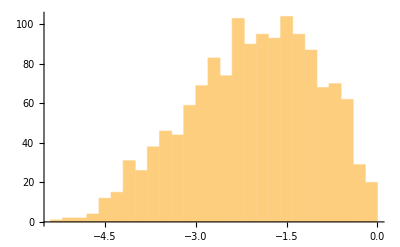

```mathematica
Histogram[Log10[cB/(nB/.densitiesWT)]/.homEqTable]
```

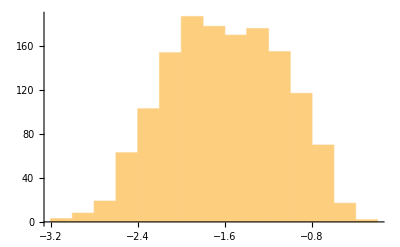

```mathematica
Histogram[Log10[cD/(nD/.densitiesWT)]/.homEqTable]
```

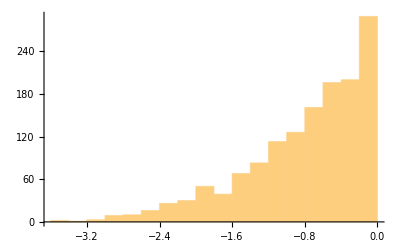

```mathematica
Histogram[Log10[cF/(nF/.densitiesWT)]/.homEqTable]
```

### Filter for Cdc42-ritC (on WT first mode set)

```mathematica
constraintCdc42ritC={{kdoff->0},1,Re@#[[2]]>minGrowth&};
```

```mathematica
filteredParams["Cdc42-ritC","WTfirstMode"]=First@Last@Reap[ParallelDo[
If[testConstraint[Join[densitiesWT,fixedParams,Thread[sampleParamNames->paramSet]],constraintCdc42ritC],
ParallelSow[paramSet]
],
{paramSet,filteredParams["WTfirstMode"]}
]
];//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{8.00667,Null}

```mathematica
Length@filteredParams["Cdc42-ritC","WTfirstMode"]
```

358

```mathematica
meanFilteredParams=10^Mean@Log10@filteredParams["Cdc42-ritC","WTfirstMode"];
```

```mathematica
meanFilteredParams
```

{0.0816379,0.11587,0.0632534,0.681785,0.0187492,0.0939873,0.200751,0.166371,0.188342,0.146316,0.10415,0.0729386,0.140431}

```mathematica
selectedParams=First@MinimalBy[filteredParams["Cdc42-ritC","WTfirstMode"],Norm[Log10@#-Log10@meanFilteredParams]&];
```

```mathematica
selectedParams
```

{0.0530652,0.346219,0.0151982,0.222098,0.00765278,0.0253192,0.166996,0.675154,0.0323169,0.288032,0.246642,0.42566,0.264606}

```mathematica
nSolveUniformEq@Join[constraintCdc42ritC[[1]],densitiesWT,fixedParams,Thread[sampleParamNames->roundSignificant[selectedParams,2]]]
```

{{mt→7.80192,md→41.0149,mg→6.46207,mtg→7.63451,mb→3.24512,mbf→3.46852,mf→1.52388,cD→0,cB→0.0195736,cF→0.921414}}

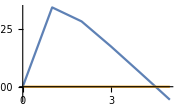
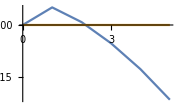
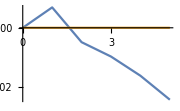
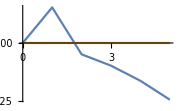
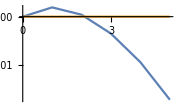
1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-

```mathematica
Row[With[{params=Join[#,densitiesWT,fixedParams,Thread[sampleParamNames->roundSignificant[selectedParams,2]]]},
With[{eqs=nSolveUniformEq@params},
Column[{
Length@eqs,
ListPlot[Transpose[Thread[{#[[1]],ReIm@#[[2]]}]&/@findDispRel[Last@eqs,params,5,"ApproxJacobian"->sphereJacobianApprox
]],Joined->True,ImageSize->Small,PlotRange->All]
},Alignment->Center]
]]&/@Join[constraints[[All,1]],{constraintCdc42ritC[[1]]}(*,constraintsCdc42OE[[All,1]]*)]
]
```

```mathematica
renderParameterGrid[filteredParams["Cdc42-ritC","WTfirstMode"],{},"selectedParams"->selectedParams]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Export/pairwise-param-scatterplot_Cdc42-ritC.png",Magnify[
renderParameterGrid[filteredParams["Cdc42-ritC","WTfirstMode"],{},
"selectedParams"->selectedParams
],
3]];
```

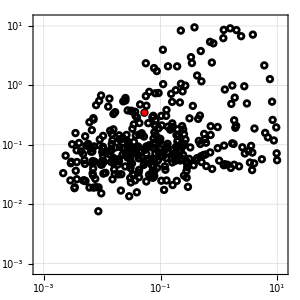

```mathematica
ListPlot[{
Log10@filteredParams["Cdc42-ritC","WTfirstMode"][[All,{1,2}]],
{Log10@selectedParams[[{1,2}]]}
},
PlotMarkers->{
{Graphics[{Black,AbsoluteThickness[2],Circle[]}],0.045},
{Graphics[{Red,Disk[]}],0.045}
},
PlotRange->{{-3.1,1.1},{-3.1,1.1}},
AspectRatio->1,
Frame->True,FrameStyle->Directive[Black,FontSize->14],
GridLines->Automatic,GridLinesStyle->GrayLevel[0.75],
FrameTicks->{{#,None},{#,None}}&@{{-3,"10^-3",{0,0.015}},{-2,"10^-2",{0,0.015}},{-1,"10^-1",{0,0.015}},{0,"10^0",{0,0.015}},{1,"10^1",{0,0.015}}},
ImageSize->300
]
```

### Filter for Cdc42-psy1^TM constraint

```mathematica
constraintCdc42TM={{kdoff->0,Dm["md"]->0.0025,Dm["mt"]->0.0025,Dm["mtg"]->0.0025,
Dm["mb"]->0.0025,Dm["mbf"]->0.0025
},1,Re@#[[2]]>0&};
```

```mathematica
filteredParams["Cdc42-psyTM","WTfirstMode"]=First@Last@Reap[ParallelDo[
If[testConstraint[Join[densitiesWT,fixedParams,Thread[sampleParamNames->paramSet]],constraintCdc42TM],
ParallelSow[paramSet]
],
{paramSet,filteredParams["Cdc42-ritC","WTfirstMode"]}
]
];
```

```mathematica
Length@filteredParams["Cdc42-psyTM","WTfirstMode"]
```

33

```mathematica
meanFilteredParams=10^Mean@Log10@filteredParams["Cdc42-psyTM","WTfirstMode"]
```

{0.098217,0.0843916,0.0363836,0.41238,0.00449562,0.13105,1.99216,0.407795,0.174052,0.14156,0.11035,0.0684217,0.0897495}

```mathematica
selectedParams=First@MinimalBy[filteredParams["Cdc42-psyTM","WTfirstMode"],Norm[Log10@#-Log10@meanFilteredParams]&];
```

```mathematica
Thread[sampleParamNames->selectedParams]
```

{ktg→0.0190906,kgt→0.0569229,kD→0.108243,kdoff→1.05705,kfd→0.00145896,kbfD→0.0439787,ktD→1.38428,ktB→0.0623689,kb→0.170318,kbF→0.43357,kbf→0.0213509,kF→0.240101,kf→0.136699}

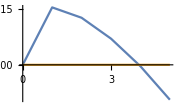
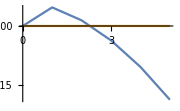
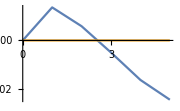
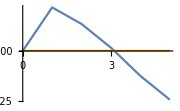
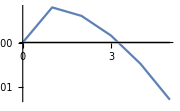
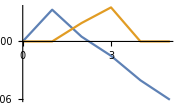
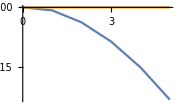
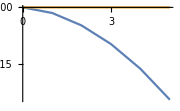
1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-

```mathematica
Row[With[{params=Join[#,densitiesWT,fixedParams,Thread[sampleParamNames->selectedParams]]},
With[{eqs=nSolveUniformEq@params},
Column[{
Length@eqs,
ListPlot[Transpose[Thread[{#[[1]],ReIm@#[[2]]}]&/@findDispRel[Last@eqs,params,5,"ApproxJacobian"->sphereJacobianApprox
]],Joined->True,ImageSize->Small,PlotRange->All]
},Alignment->Center]
]]&/@Join[constraints[[All,1]],{constraintCdc42ritC[[1]],constraintCdc42TM[[1]]},constraintsCdc42OE[[All,1]]]
]
```

```mathematica
renderParameterGrid[filteredParams["Cdc42-ritC","WTfirstMode"],filteredParams["Cdc42-psyTM","WTfirstMode"]]
```

-Graphics-

### Filter for Cdc42-TM constraint (on “core set”)

```mathematica
filteredParams["Cdc42-psyTM"]=First@Last@Reap[ParallelDo[
If[testConstraint[Join[densitiesWT,fixedParams,Thread[sampleParamNames->paramSet]],constraintCdc42TM],
ParallelSow[paramSet]
],
{paramSet,matchParams}
]
];
```

```mathematica
Length@filteredParams["Cdc42-psyTM"]
```

155

```mathematica
meanFilteredParams=10^Mean@Log10@filteredParams["Cdc42-psyTM"]
```

{0.328082,0.290321,0.0298783,0.577143,0.0134352,0.292422,2.07048,0.618729,0.280491,0.233638,0.11365,0.0892333,0.0915847}

```mathematica
selectedParams=First@MinimalBy[filteredParams["Cdc42-psyTM"],Norm[Log10@#-Log10@meanFilteredParams]&];
```

```mathematica
Thread[sampleParamNames->roundSignificant[selectedParams,2]]
```

{ktg→0.36,kgt→1.5,kD→0.0017,kdoff→0.82,kfd→0.052,kbfD→0.3,ktD→1.,ktB→2.1,kb→0.23,kbF→0.057,kbf→0.03,kF→0.017,kf→0.046}

```mathematica
nSolveUniformEq@Join[constraintCdc42TM[[1]],densitiesWT,fixedParams,Thread[sampleParamNames->selectedParams]]
```

{{mt→13.3516,md→32.2777,mg→3.27456,mtg→10.822,mb→2.23703,mbf→4.47735,mf→0.379163,cD→0,cB→0.0189415,cF→1.03788}}

```mathematica
Thread[sampleParamNames->roundSignificant[meanFilteredParams,2]]
```

{ktg→0.33,kgt→0.29,kD→0.03,kdoff→0.58,kfd→0.013,kbfD→0.29,ktD→2.1,ktB→0.62,kb→0.28,kbF→0.23,kbf→0.11,kF→0.089,kf→0.092}

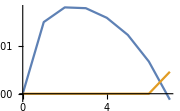
{mt→11.905,md→31.4187,mg→0.969032,mtg→13.1275,mb→2.38302,mbf→4.24799,mf→0.824749,cD→0,cB→0.0903994,cF→0.852549}
-Graphics-

```mathematica
With[{
params=Join[constraintCdc42TM[[1]],densitiesWT,fixedParams,Thread[sampleParamNames->roundSignificant[meanFilteredParams,2]]]
},
Column[{
Last@nSolveUniformEq@params,
ListPlot[Transpose[Thread[{#[[1]],ReIm@#[[2]]}]&/@findDispRel[Last@nSolveUniformEq@params,params,7,"ApproxJacobian"->sphereJacobianApprox
]],Joined->True,ImageSize->Small,PlotRange->All]
}]
]
```

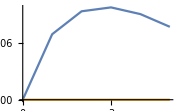
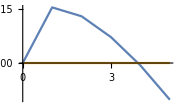
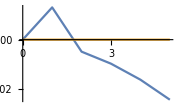
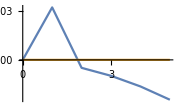
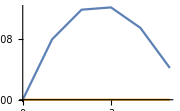
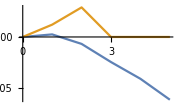
1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-1
-Graphics-

```mathematica
Row[With[{params=Join[#,densitiesWT,fixedParams,Thread[sampleParamNames->selectedParams]]},
With[{eqs=nSolveUniformEq@params},
Column[{
Length@eqs,
ListPlot[Transpose[Thread[{#[[1]],ReIm@#[[2]]}]&/@findDispRel[Last@eqs,params,5,"ApproxJacobian"->sphereJacobianApprox
]],Joined->True,ImageSize->Small,PlotRange->All]
},Alignment->Center]
]]&/@Join[constraints[[All,1]],{constraintCdc42ritC[[1]],constraintCdc42TM[[1]]}]
]
```

```mathematica
renderParameterGrid[filteredParams["Cdc42-psyTM"],{},"selectedParams"->meanFilteredParams]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Export/pairwise-param-scatterplot_Cdc42-TM.png",Magnify[
renderParameterGrid[filteredParams["Cdc42-psyTM"],{},"selectedParams"->selectedParams],
3]];
```